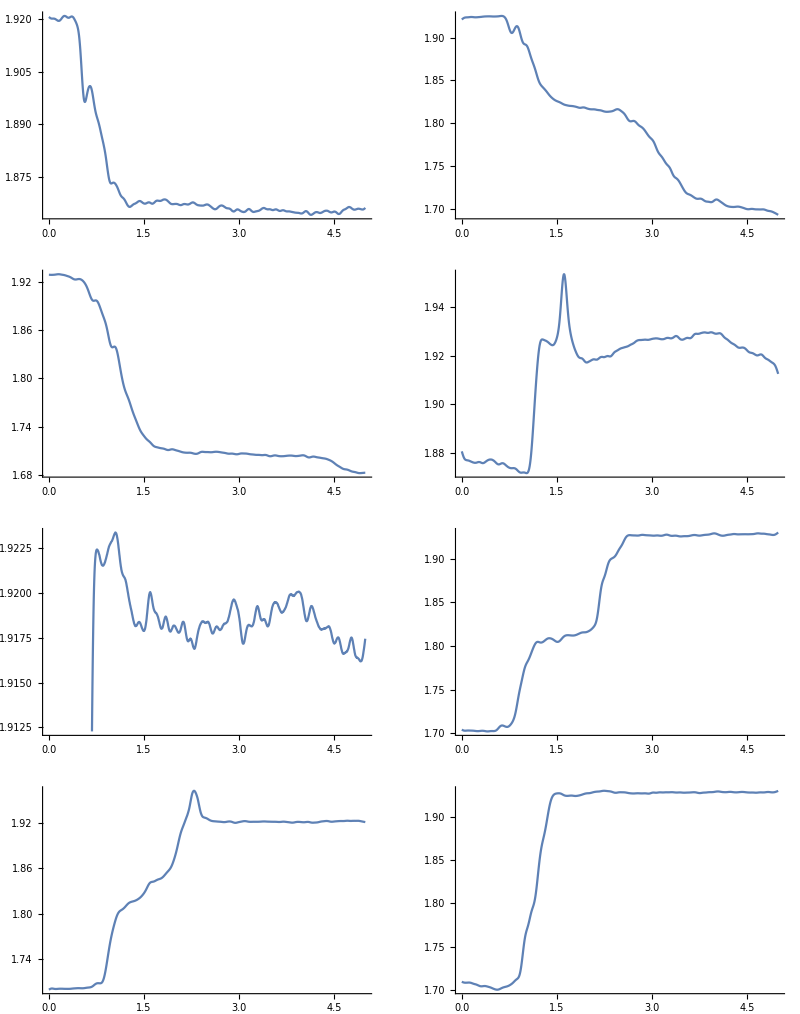

```mathematica
SetDirectory[NotebookDirectory[]<>".."];
comercialFileList=FileNames["Data/Comercial_*.lvm"];

ComecialPlot[dataIn_]:=(
data=dataIn;
frequency=1/(data[[2, 1]]-data[[1, 1]]);
data[[All, 2]]=LowpassFilter[data[[All, 2]], 20/frequency];
ListPlot[data, Joined->True]
);

data=Import[#, "TSV",NumberPoint->","]& /@ comercialFileList;

plots=ComecialPlot/@data;
Export["Images/Comercial.pdf",GraphicsGrid[Partition[plots, 2]]];
GraphicsGrid[Partition[plots, 2], ImageSize->Full]
```